```mathematica
L=1.;
δx=0.1;
δt=0.01;
a=0.1;
```

```mathematica
Clear[u]
u[0.,_]:=0.
u[1.,_]:=1.
u[x_,0.]:=100.x(1.-x)
u[x_,t_?Positive]:=u[x,t]=u[x,t-δt](1-(2 a^2 δt)/δx^2)+(a^2 δt)/δx^2(u[x+δx,t-δt]+u[x-δx,t-δt])
```

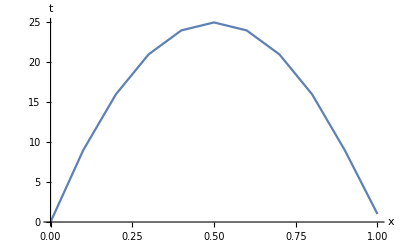

```mathematica
ListLinePlot[{#,u[#,0.]}&/@Range[0,L,δx],AxesLabel->{"x","t"}]
```

```mathematica
ListLinePlot[Table[{#,u[#,t]}&/@Range[0,L,δx],{t,Range[0,2,0.2]}],AxesLabel->{"x","t"}]
```

$Aborted